### Необходимые функции

```mathematica
ClearAll[F,r2,φ,X,Y];
```

```mathematica
F[n_,r1_,r2_]:=1/((n-1)(r2-r1));
r2[n_,r1_,F_] := 1/(F(n-1))+r1;
φ[n0_,r_,φin_,y_]:=ArcSin[n0 Sin[φin-ArcSin[y r]]]+ArcSin[y r];
X[F_,φout_,y_]:=2F -y 1/Tan[-φout];
Y[F_,φout_,y_]:=2F Tan[-φout]-y;
```

```mathematica
r2[1.5,0,1]
```

2.

```mathematica
2.
```

2.

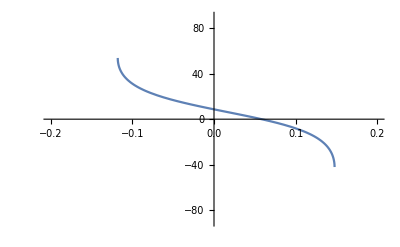

```mathematica
Plot[φ[1.5,r,0.1,5]/π*180,{r,-0.2,0.2},PlotRange->{{-0.2,0.2},{-90,90}}]
```

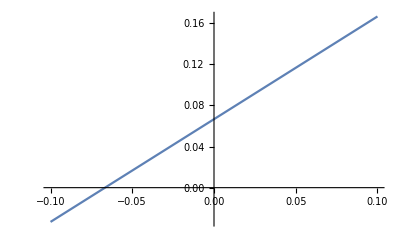

```mathematica
Plot[r2[n,r1,30],{r1,-0.1,0.1}]
```

```mathematica
n=1.5;H=10; F0=30; r1=0;
a=φ[n,r2[n,r1,F0],φ[1/n,r1,ArcTan[H/(4 F0)],H/2],H/2]
```

-0.0946412

```mathematica
1/Tan[a]*H/2
```

-52.6733

```mathematica
X[F0,a,5]
```

7.32674

### График

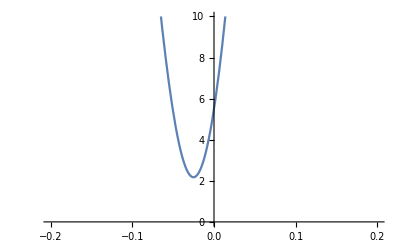

```mathematica
H=10;F0=40;n=1.5;
Plot[
X[F0,φ[n,r2[n,r1,F0],φ[1/n,r1,ArcTan[H/(4 F0)],H/2],H/2],H/2],
{r1,-0.1,0.1},PlotRange->{{-0.2,0.2},{0,10}}
]
```

```mathematica
ClearAll[r1,r2,H,F0]
```

```mathematica
ClearAll[r1]
```

```mathematica
Manipulate[
Grid[
{
{
Plot[
X[F0,φ[n,r2[n,r1,F0],φ[1/n,r1,ArcTan[H/(4 F0)],H/2],H/2],H/2],
{r1,-0.1,0.1},PlotRange->{{-0.1,0.1},{0,10}},GridLines->{Range[-0.1,0.1,0.01], Range[0,20,0.5]},
Ticks->{Range[-0.1,0.1,0.02],Range[0,10,1]},
ImageSize->400
]
},
{
min=FindMinimum[
X[F0,φ[n,r2[n,r1,F0],φ[1/n,r1,ArcTan[H/(4 F0)],H/2],H/2],H/2]
,{r1,-0.1,0.1}]
},
{
"r_2= "<>ToString[r2[n,r1/.min⟦2⟧,F0]]
}
}
],
{{F0,40,"F_0"},0,100},
{{H,10,"H"},1,20},
{{n,1.5,"n"},1.001,3}
]
```

## ППП

```mathematica
Manipulate[
Grid[
{
{
(* Продольная абберация, если первая поверхность плоская *)
XP1=X[F0,φ[n,r2[n,0,F0],φ[1/n,0,ArcTan[H/(4 F0)],H/2],H/2],H/2];
"(:041f)_x(0)= "<>ToString[XP1]
},
{(* Поперечная абберация, если первая поверхность плоская *)
YP1 = Y[F0,φ[n,r2[n,0,F0],φ[1/n,0,ArcTan[H/(4 F0)],H/2],H/2],H/2];
"(:041f)_y(0)= "<>ToString[YP1]
},
{
XP2=X[F0,φ[n,r2[n,1/(F0(1-n)),F0],φ[1/n,1/(F0(1-n)),ArcTan[H/(4 F0)],H/2],H/2],H/2]
},
{
YP2=Y[F0,φ[n,r2[n,1/(F0(1-n)),F0],φ[1/n,1/(F0(1-n)),ArcTan[H/(4 F0)],H/2],H/2],H/2]
},
{
r2[n,1/(F0(1-n)),F0]
}
}
],

{{F0,40,"F_0"},0,100},
{{H,10,"H"},1,20},
{{n,1.5,"n"},1.001,3}
]
```

```mathematica
Manipulate[
Grid[
{
{
Plot[X[F0,φ[n,r2[n,1/(F0(1-n)),F0],φ[1/n,1/(F0(1-n)),ArcTan[H/(4 F0)],H/2],H/2],H/2],{F0,0,100}]
},
{
Plot[Y[F0,φ[n,r2[n,1/(F0(1-n)),F0],φ[1/n,1/(F0(1-n)),ArcTan[H/(4 F0)],H/2],H/2],H/2],{F0,0,100}]
},
{
r2[n,1/(F0(1-n)),F0]
}
}
],
{{H,10,"H"},1,20},
{{n,1.5,"n"},1.001,3}
]
```

## Пункт 2

```mathematica
ClearAll[F1,F2,r1,r2,F]
```

```mathematica
F[n_,r1_,r2_]:=1/((n-1)(r2-r1));
R2[n_,r1_,F_] := 1/(F(n-1))+r1;
φ[n0_,r_,φin_,y_]:=ArcSin[n0 Sin[φin-ArcSin[y r]]]+ArcSin[y r];
X[F_,φout_,y_]:=2F -y 1/Tan[-φout];
Y[F_,φout_,y_]:=2F Tan[-φout]-y;
```

```mathematica
PX[r1_,r2_,ρ1_,n1_,n2_,F0_,H_] := X[F0,
φ[
n2,
R2[n2,ρ1,(F[n1,r1,r2] F0)/(F[n1,r1,r2]-F0)],
φ[
1/n2,
ρ1,
φ[
n1,
r2,
φ[1/n1,
r1,
ArcTan[H/(4F0)],
H/2],
H/2],
H/2],
H/2],
H/2];
```

```mathematica
ClearAll[ρ1,n1,n2]
F0=40;H=10;
r1=-0.02;r2=0.02;n1=1.5;n2=1.5;
```

```mathematica
F[n1,r1,r2]
```

50.

```mathematica
ClearAll[r1,r2,ρ1,n1,n2]
```

```mathematica
FindMinimum[
{PX[r1,r2,ρ1,n1,n2,F0,H],r1≠r2},
{r1,-0.01,0.01},
{r2,0,0.03},
{ρ1,-0.01,0.01},
{n1,1.1,2},
{n2,1.1,2}
]
```

FindMinimum::eqineq: Constraints in {r2≠r1} are not all equality or inequality constraints. With the exception of integer domain constraints for linear programming, domain constraints or constraints with Unequal (!=) are not supported.

FindMinimum[{PX[r1,r2,ρ1,n1,n2,F0,H],r1≠r2},{r1,-0.01,0.01},{r2,0,0.03},{ρ1,-0.01,0.01},{n1,1.1,2},{n2,1.1,2}]

```mathematica
FindMinimum[Sin[x]Sin[2y],{{x,2},{y,2}}]
```

{-1.,{x→1.5708,y→2.35619}}

```mathematica
ClearAll[r1,r2,n2]
```

```mathematica
F0=40;H=10;
n1=1.5;n2=2;
min=FindMinimum[
{PX[r1,r2,ρ1,n1,n2,F0,H],
-0.1≤r1≤0.1,
-0.1≤r2≤0.1,
-0.1≤ρ1≤0.1,
r1<r2},
{r1,-0.01},
{r2,0},
{ρ1,-0.01}
]
```

{0.535024,{r1→-0.00438589,r2→0.0141663,ρ1→-0.0106728}}

```mathematica
min⟦2,3⟧
```

ρ1→-0.0106728

```mathematica
R2[n2,ρ1/.min⟦2,3⟧,(F[n1,r1/.min⟦2,1⟧,r2/.min⟦2,2⟧] F0)/(F[n1,r1/.min⟦2,1⟧,r2/.min⟦2,2⟧]-F0)]
```

0.00505108

```mathematica
F[n1,r1,r2]
```

2./(-r1+r2)

```mathematica
(F[n1,r1,r2] F0)/(F[n1,r1,r2]-F0)
```

80./((-r1+r2) (-40+2./(-r1+r2)))

## 1*

```mathematica
Yk[k_]:=Y[F0,φ[n,r2[n,r1,F0],φ[1/n,r1,ArcTan[(H*k)/(4 F0*K)],(H*k)/(2*K)],(H*k)/(2*K)],(H*k)/(2*K)];
Xk[k_]:=X[F0,φ[n,r2[n,r1,F0],φ[1/n,r1,ArcTan[(H*k)/(4 F0*K)],(H*k)/(2*K)],(H*k)/(2*K)],(H*k)/(2*K)];
```

```mathematica
Ik[k_]:=I0*1/(K^2+((H k)/(4F))^2)*(2k+1)/(Yk[k]-Yk[k-1]);
```

```mathematica
I0 = 1; K=10; H=10;F=40;r1=-0.001;
```

```mathematica
Yk[0]
```

0.

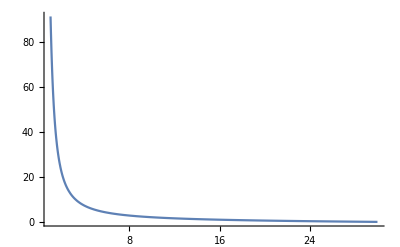

```mathematica
Plot[Ik[k],{k,1,30},PlotRange->All]
```

```mathematica
Range[1,10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Yk/@Range[1,10]
```

{0.000328925,0.00263635,0.00892571,0.0212511,0.0417446,0.0726461,0.116337,0.175378,0.252556,0.350936}

```mathematica
Map[Yk,Range[1,10]]
```

{0.000328925,0.00263635,0.00892571,0.0212511,0.0417446,0.0726461,0.116337,0.175378,0.252556,0.350936}

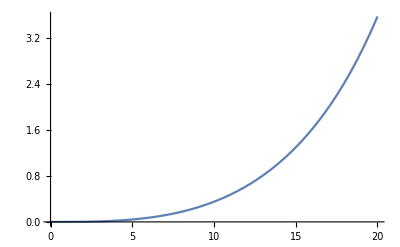

```mathematica
Plot[Yk[k],{k,0,20}]
```

```mathematica
(Xk[1]-Xk[K])*Tan[φ[1/n,r1,ArcTan[(H*1)/(4 F0*K)],(H*1)/(2*K)]]
```

-0.0207762

```mathematica
FindMinimum[(Xk[k]-Xk[15])*Tan[φ[1/n,r1,ArcTan[(H*k)/(4 F0*K)],(H*k)/(2*K)]],{k,1,100}]
```

{-0.272034,{k→8.65425}}

```mathematica
Min[Table[(Xk[k]-Xk[15])*Tan[φ[1/n,r1,ArcTan[(H*k)/(4 F0*K)],(H*k)/(2*K)]],{k,1,K}]]
```

-0.271376

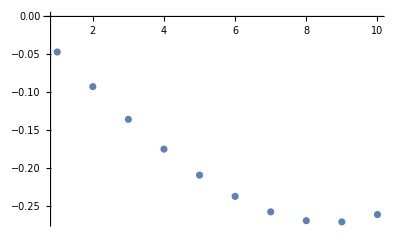

```mathematica
ListPlot[Table[(Xk[k]-Xk[15])*Tan[φ[1/n,r1,ArcTan[(H*k)/(4 F0*K)],(H*k)/(2*K)]],{k,1,K}],PlotRange->All]
```

### Создание цвета

```mathematica
K=100;
```

```mathematica
data =Ik/@Range[1,K];
```

```mathematica
data⟦1⟧
```

912.628

```mathematica
data⟦9⟧
```

26.615

```mathematica
colornorm = 1/(Max[data]-Min[data])*(data-Min[data]);
```

```mathematica
color = Hue[0.1,#,1]&/@ colornorm;
```

```mathematica
coloryan1 = Hue[1,#,1]&/@(1/π*ArcTan[data]+1/2);
```

```mathematica
disks =Disk[{0,0},#]&/@Map[Yk,Range[1,K]];
```

```mathematica
colordisks=Reverse[Table[List[color⟦i⟧,disks⟦i⟧],{i,1,K}]];
```

```mathematica
Manipulate[
Grid[{{
Graphics[colordisks⟦-n;;⟧],
Plot[Ik[k],{k,1,K},AxesLabel->{"K","I"},PlotRange->{{0,100},{0,1000}}],
Plot[Yk[k],{k,1,K},AxesLabel->{"K","R"},PlotRange->{{0,100},{0,Yk[K]}}]
}}],
{n,1,K,1}
]
```